## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

myVerify [varSet_,flowVec_,initBoundary_,unsafeBoundary_,bc_,deg_,numTolerance_]:= Module[
{lambda,unsafeCons,initCons,bcLie,bc1,bc2,bc3,bc4,timev,range},
timev=Now;
lambda = -1;
unsafeCons = And@@(GreaterEqual[#,0]&/@unsafeBoundary);
initCons = And@@(GreaterEqual[#,0]&/@initBoundary);
If[Length[varSet]==2,
bcLie =D[bc,varSet[[1]]]*flowVec[[1]]+D[bc,varSet[[2]]]*flowVec[[2]],
bcLie =D[bc,varSet[[1]]]*flowVec[[1]]+D[bc,varSet[[2]]]*flowVec[[2]] + D[bc,varSet[[3]]]*flowVec[[3]];
];

bc1 = FindInstance[bc>0&&initCons,varSet];
bc2 =FindInstance[bc≤ 0&&unsafeCons,varSet];
bc3 =FindInstance[bcLie-lambda*bc> 0,varSet];
bc4 =FindInstance[bc== 0&&bcLie> 0,varSet];

If[Or[Length[bc1]+Length[bc2]+Length[bc3]==0,Length[bc1]+Length[bc2]+Length[bc4]==0],
Return[1]];
If[numTolerance==1,
range =  Total[varSet^2]<= 1000000;
bc1 = FindInstance[bc>0&&initCons&&range,varSet];
bc2 =FindInstance[bc≤ 0&&unsafeCons&&range,varSet];
bc3 =FindInstance[bcLie-lambda*bc> 0&&range,varSet];
bc4 =FindInstance[bc== 0&&bcLie> 0&&range,varSet];

If[Or[Length[bc1]+Length[bc2]+Length[bc3]==0,Length[bc1]+Length[bc2]+Length[bc4]==0],
Return[1]];
];
Return[0]
]

verifyResults[benchmark_,plot_,plotRange_,verifyTime_,numTolerance_]:= Module[
{systemPath,varSet,flowVec,initCons,unsafeCons,bcPath,bcData,ebc,hbc,ebcDeg,hbcDeg,totaltime,totalsdptime,time,etime,htime,ptime,result,i,sbc,sbcDeg},
systemPath=FileNameJoin[{".","Results","systems",StringJoin[benchmark,".txt"]}];
{varSet,flowVec,initCons,unsafeCons} = ReadList[systemPath];
ebcDeg=0;
hbcDeg=0;
Print["Variables: ",varSet];
Print["Flow: ",flowVec];
Print["Initial: ",initCons];
Print["Unsafe: ",unsafeCons];

Print[Style["Using Bounded Case Characterization: ", Blue]];
bcPath=FileNameJoin[{".","Results","sound",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ Length[bcData],i++,
ebc = bcData[[i]][[1]];
time = bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,ebc,i,numTolerance],verifyTime,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime +time;
If[result[[2]]== 1,
ebcDeg=i;
Print["Verified at deg ", i];
Print[ebc];
Break[]
];
If[result[[2]]== 2,
Print["Verify out of time at deg ", i];
ebcDeg=0;
Print[ebc];
Break[]
];
];
etime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[ebcDeg>0,
Print["Using Sound Characterization: Verified, time used: ",etime];,
Print["Using Sound Characterization: No valid soltion, time used: ",etime];
];

Print[Style["Using Complete (polynomial) Characterization:", Blue]];
bcPath=FileNameJoin[{".","Results","complete",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ Length[bcData],i++,
hbc = bcData[[i]][[1]];
time =bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,hbc,i,numTolerance],verifyTime,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + time;
If[result[[2]]== 1,
hbcDeg=i;
Print["Verified at deg ", i];
Print[hbc];
Break[]
];
If[result[[2]]== 2,
Print["Verify out of time at deg ", i];
hbcDeg=0;
Print[hbc];
Break[]
];
];
htime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[hbcDeg>0,
Print["Using Complete (polynomial) Characterization: Verified, time used: ",htime];,
Print["Using Complete (polynomial) Characterization: No valid soltion, time used: ",htime];
];

Print[Style["Using Complete (semialgebraic) Characterization:", Blue]];
bcPath=FileNameJoin[{".","Results","completesemi",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ Length[bcData],i++,
sbc = bcData[[i]][[1]];
time =bcData[[i]][[2]];
sbc = sbc/.u-> Sqrt[Total[varSet^2]+1];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,sbc,i,numTolerance],verifyTime,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + time;
If[result[[2]]== 1,
sbcDeg=i;
Print["Verified at deg ", i];
Print[sbc];
Break[]
];
If[result[[2]]== 2,
Print["Verify out of time at deg ", i];
Print[sbc];
sbcDeg=0;
Break[]
];
];
htime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[sbcDeg>0,
Print["Using Complete (semialgebraic) Characterization: Verified, time used: ",htime],
Print["Using Complete (semialgebraic) Characterization: No valid soltion, time used: ",htime]
];
If[ plot== 1,
If[Length[varSet]== 2,myPlot2D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc],If[sbcDeg== 0,1,sbc]]];
If[Length[varSet]== 3,myPlot3D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc],If[sbcDeg== 0,1,sbc]]];
]
]
myPlot2D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_,sbc_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot,sbcPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
sampleNum = 5;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
bcPlot=RegionPlot[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
bchPlot=RegionPlot[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
sbcPlot=RegionPlot[sbc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.6900000000000001, 0.52, 0.6900000000000001]},BoundaryStyle->{RGBColor[0.6900000000000001, 0.52, 0.6900000000000001]},PlotPoints-> 100];
Print[Show[flowPlot,initPlot,unsafePlot,trajPlot,bcPlot,bchPlot,sbcPlot, FrameLabel->varSet]]
]

myPlot3D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_,sbc_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot,sbcPlot},
Print["Plot3d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
(*flowPlot =VectorPlot3D[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->{Opacity[0.4],Gray}];*)
(*plot init and unsafe regions*)
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot3D[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100,Mesh->None];
unsafePlot=RegionPlot3D[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100,Mesh->None];
(*plot sample trajectories*)
sampleNum = 5;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]]&&varRange[[3]][[1]]≤ varSet[[3]]≤ varRange[[3]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];trajPlot=ParametricPlot3D[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
bcPlot=RegionPlot3D[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.3],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100,Mesh->None];
bchPlot=RegionPlot3D[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.3],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100,Mesh->None];
sbcPlot=RegionPlot3D[sbc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.3],RGBColor[0.6900000000000001, 0.52, 0.6900000000000001]},BoundaryStyle->{RGBColor[0.6900000000000001, 0.52, 0.6900000000000001]},PlotPoints-> 100,Mesh->None];
Print[Show[initPlot,unsafePlot,trajPlot,bcPlot,bchPlot,sbcPlot, FrameLabel->varSet]]
];
```

## Benchmarks

### 2-dim benchmarks

arch3-2

Variables: {x1,x2}

Flow: {x1-x1^3+x2-x1 x2^2,-x1+x2-x1^2 x2-x2^3}

Initial: {-2+x1-x2^2,x2,x1}

Unsafe: {-2-x1^2-x2,-x2}

Using Bounded Case Characterization:

totalsdptime: 0.0651655

Using Sound Characterization: No valid soltion, time used: 2.35051

Using Complete (polynomial) Characterization:

totalsdptime: 0.231082

Using Complete (polynomial) Characterization: No valid soltion, time used: 3.86412

Using Complete (semialgebraic) Characterization:

Verified at deg 1

-0.00046-0.00005 x1-0.00025 x2

totalsdptime: 0.417221

Using Complete (semialgebraic) Characterization: Verified, time used: 0.422915

Plot2d...

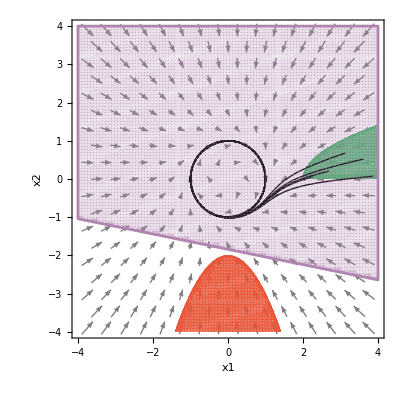

```mathematica
benchmarkname = "arch3-2";
Print[benchmarkname];
verifytime=60;
plot =1;
plotRange = {{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytime,1]
```

vector-1

Variables: {x1,x2}

Flow: {x2,x1}

Initial: {4+x1,4+x2,-x1,-x2}

Unsafe: {-6-4 x1-x1^2+4 x2-x2^2}

Using Bounded Case Characterization:

Verified at deg 4

-2.58094-0.16151 x1+0.15753 x1^2-0.01854 x1^3-0.13581 x1^4+1.60903 x2-2.59865 x1 x2+0.16366 x1^2 x2-0.21102 x1^3 x2-0.11131 x2^2+0.5626 x1 x2^2-0.16758 x1^2 x2^2+0.38036 x2^3-0.24536 x1 x2^3-0.15298 x2^4

totalsdptime: 0.0175586

Using Sound Characterization: Verified, time used: 0.608135

Using Complete (polynomial) Characterization:

Verified at deg 3

-3.8487-0.47379 x1+0.67093 x1^2+0.42297 x1^3+2.64218 x2-4.01469 x1 x2-0.42297 x1^2 x2-0.18874 x2^2-0.42297 x1 x2^2+0.42297 x2^3

totalsdptime: 0.023054

Using Complete (polynomial) Characterization: Verified, time used: 0.037438

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-4.29425-1.58033 x1-0.18484 x1^2+2.11683 x2-2.92479 x1 x2-0.21861 x2^2-2.5388 √(1+x1^2+x2^2)-0.42778 x1 √(1+x1^2+x2^2)-0.43225 x1^2 √(1+x1^2+x2^2)+2.63616 x2 √(1+x1^2+x2^2)-2.3902 x1 x2 √(1+x1^2+x2^2)-0.23934 x2^2 √(1+x1^2+x2^2)

totalsdptime: 0.225035

Using Complete (semialgebraic) Characterization: Verified, time used: 0.964496

Plot2d...

-Graphics-

vector-2

Variables: {x1,x2}

Flow: {x2,x1}

Initial: {-1+x1 x2}

Unsafe: {-2-x1,-2+x2}

Using Bounded Case Characterization:

totalsdptime: 0.0349668

Using Sound Characterization: No valid soltion, time used: 0.372237

Using Complete (polynomial) Characterization:

Verified at deg 4

-1.20177-0.08537 x1-0.4637 x1^2+0.08539 x2-1.56778 x1 x2+0.10133 x1^2 x2-1.34473 x1^3 x2-0.46554 x2^2-0.10137 x1 x2^2+0.49659 x1^2 x2^2-1.34515 x1 x2^3

totalsdptime: 0.0340952

Using Complete (polynomial) Characterization: Verified, time used: 0.190903

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-2.20535-0.71153 x1-1.04651 x1^2+0.71155 x2-1.3128 x1 x2-1.04653 x2^2-1.40411 √(1+x1^2+x2^2)-0.14932 x1 √(1+x1^2+x2^2)+0.14932 x2 √(1+x1^2+x2^2)-2.1496 x1 x2 √(1+x1^2+x2^2)

totalsdptime: 0.239223

Using Complete (semialgebraic) Characterization: Verified, time used: 0.825044

Plot2d...

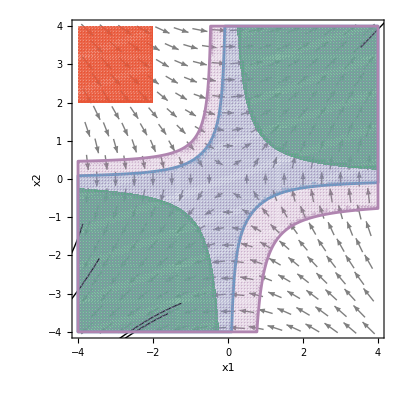

barrier-1

Variables: {x1,x2}

Flow: {x2,-x1+0.333 x1^3-x2}

Initial: {-2.+3. x1-x1^2-x2^2}

Unsafe: {-1.84-2. x1-x1^2-2. x2-x2^2}

Using Bounded Case Characterization:

totalsdptime: 0.914744

Using Sound Characterization: No valid soltion, time used: 2.59919

Using Complete (polynomial) Characterization:

totalsdptime: 1.15746

Using Complete (polynomial) Characterization: No valid soltion, time used: 2.98609

Using Complete (semialgebraic) Characterization:

totalsdptime: 15.8997

Plot2d...

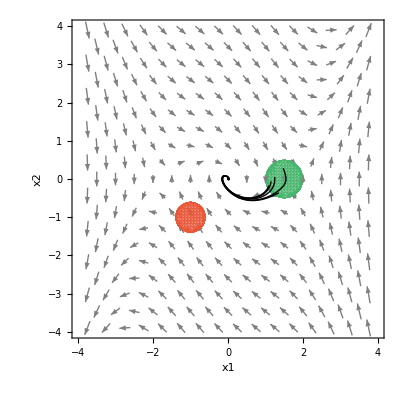

barrier-2

Variables: {x1,x2}

Flow: {x2,-x1+0.333333 x1^3-x2}

Initial: {-1.+x1 x2,x1}

Unsafe: {-2.-x1,-2.+x2}

Using Bounded Case Characterization:

totalsdptime: 0.0427828

Using Sound Characterization: No valid soltion, time used: 0.815515

Using Complete (polynomial) Characterization:

Verified at deg 3

-0.00278-0.00068 x1-0.00019 x1^2-0.00013 x1^3-0.00006 x2-0.00041 x1 x2

totalsdptime: 0.0341044

Using Complete (polynomial) Characterization: Verified, time used: 0.0444944

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-4.49404-1.11159 x1-4.49596 x1^2+0.12596 x2-3.36716 x1 x2-2.91943 x2^2-3.14317 √(1+x1^2+x2^2)+0.00223 x1 √(1+x1^2+x2^2)+0.09803 x2 √(1+x1^2+x2^2)-4.548 x1 x2 √(1+x1^2+x2^2)

totalsdptime: 2.30448

Using Complete (semialgebraic) Characterization: Verified, time used: 3.36568

Plot2d...

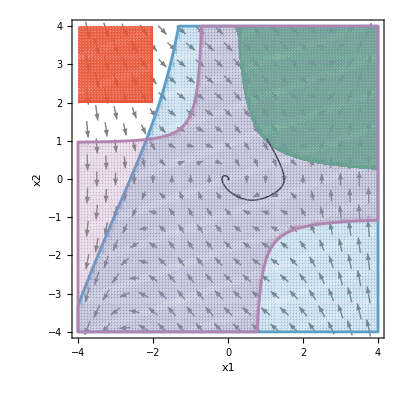

lie-der-1

Variables: {x1,x2}

Flow: {-2. x2,x1^2}

Initial: {-0.84-2. x1-x1^2-x2^2}

Unsafe: {-0.84-x1^2-2. x2-x2^2}

Using Bounded Case Characterization:

Verified at deg 3

-0.45775+0.12792 x1-0.3157 x1^2+0.12474 x1^3-0.61209 x2+0.556 x1 x2-0.37578 x1^2 x2+0.32375 x2^2-0.27525 x1 x2^2-0.5505 x2^3

totalsdptime: 0.0599839

Using Sound Characterization: Verified, time used: 0.241764

Using Complete (polynomial) Characterization:

Verified at deg 3

-1.00017+0.12068 x1-0.67243 x1^2+0.08588 x1^3-1.60464 x2+1.04012 x1 x2-0.64411 x1^2 x2+0.23896 x2^2-0.40852 x1 x2^2-0.81704 x2^3

totalsdptime: 0.0713154

Using Complete (polynomial) Characterization: Verified, time used: 0.220977

Using Complete (semialgebraic) Characterization:

Verified at deg 1

-0.00559+0.00554 x1-0.01862 x2-0.01057 √(1+x1^2+x2^2)-0.00863 x1 √(1+x1^2+x2^2)-0.00995 x2 √(1+x1^2+x2^2)

totalsdptime: 0.348594

Using Complete (semialgebraic) Characterization: Verified, time used: 0.834385

Plot2d...

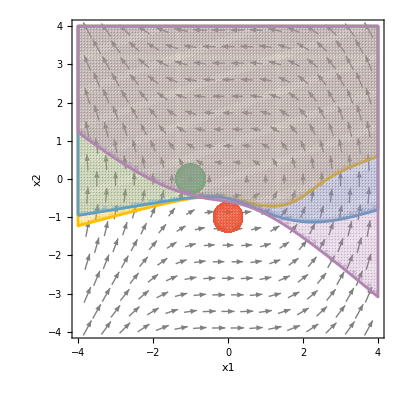

lie-der-2

Variables: {x1,x2}

Flow: {-2. x2,x1^2}

Initial: {1.-x2^2,-1.-x1}

Unsafe: {-2.+x1-0.04 x2^2,x1}

Using Bounded Case Characterization:

Verified at deg 3

-3.19181+0.81008 x1-0.27644 x1^2+0.37178 x1^3-1.84001 x2+1.08989 x1 x2-0.2491 x1^2 x2+1.17507 x2^2-0.04095 x1 x2^2-0.08189 x2^3

totalsdptime: 0.0129215

Using Sound Characterization: Verified, time used: 0.153841

Using Complete (polynomial) Characterization:

Verified at deg 3

-4.50064+1.17989 x1-0.26328 x1^2+0.44346 x1^3-2.66376 x2+1.51359 x1 x2-0.32951 x1^2 x2+1.47713 x2^2-0.0479 x1 x2^2-0.0958 x2^3

totalsdptime: 0.022339

Using Complete (polynomial) Characterization: Verified, time used: 0.21628

Using Complete (semialgebraic) Characterization:

Verified at deg 3

-6.89682+3.26361 x1-3.83391 x1^2+0.21561 x1^3-0.42599 x2+0.4012 x1 x2-3.52551 x1^2 x2-2.70272 x2^2-0.17546 x1 x2^2-2.25946 x2^3-3.62091 √(1+x1^2+x2^2)+2.75063 x1 √(1+x1^2+x2^2)-1.17876 x1^2 √(1+x1^2+x2^2)+1.32407 x1^3 √(1+x1^2+x2^2)-3.29596 x2 √(1+x1^2+x2^2)+5.10851 x1 x2 √(1+x1^2+x2^2)-0.62706 x1^2 x2 √(1+x1^2+x2^2)+3.71129 x2^2 √(1+x1^2+x2^2)-0.09248 x1 x2^2 √(1+x1^2+x2^2)-0.16028 x2^3 √(1+x1^2+x2^2)

totalsdptime: 2.44148

Using Complete (semialgebraic) Characterization: Verified, time used: 4.66027

Plot2d...

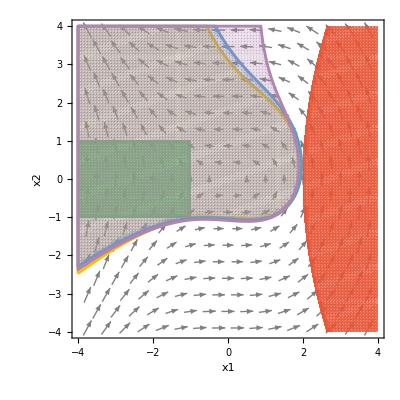

arch1-1

Variables: {x1,x2}

Flow: {-x1+2. x1^3 x2^2,-x2}

Initial: {-3.75-x1^2+4. x2-x2^2}

Unsafe: {-16.59-6. x1-x1^2+5.6 x2-x2^2}

Using Bounded Case Characterization:

Verified at deg 4

-2.63161+0.02362 x1-0.00573 x1^2+0.0001 x1^3-0.00009 x1^4+1.05954 x2-0.01176 x1 x2+0.0087 x1^2 x2-0.00277 x1^3 x2+0.35199 x2^2-0.10748 x1 x2^2-0.03245 x1^2 x2^2-0.51435 x2^3-0.00001 x1 x2^3+0.14782 x2^4

totalsdptime: 0.0838773

Using Sound Characterization: Verified, time used: 0.380379

Using Complete (polynomial) Characterization:

Verified at deg 4

-6.69958+0.05565 x1-0.01189 x1^2+0.00067 x1^3-0.00013 x1^4+3.2237 x2-0.0145 x1 x2+0.02847 x1^2 x2-0.00443 x1^3 x2+1.1289 x2^2-0.17666 x1 x2^2-0.0572 x1^2 x2^2-1.37107 x2^3+0.00002 x1 x2^3+0.33113 x2^4

totalsdptime: 0.173604

Using Complete (polynomial) Characterization: Verified, time used: 0.476879

Using Complete (semialgebraic) Characterization:

totalsdptime: 108.579

Plot2d...

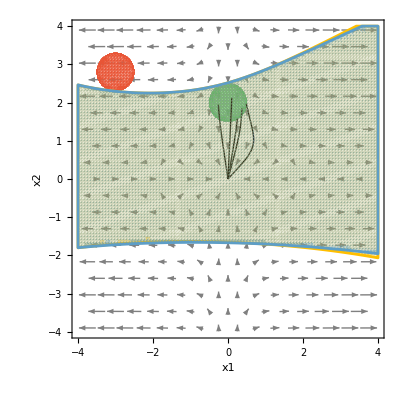

arch1-2

Variables: {x1,x2}

Flow: {-x1+2 x1^3 x2^2,-x2}

Initial: {1-x1^2,-2+x2}

Unsafe: {1-x1^2,-2-x2}

Using Bounded Case Characterization:

Verified at deg 1

-0.96803-1.11154 x2

totalsdptime: 0.00903963

Using Sound Characterization: Verified, time used: 0.0118236

Using Complete (polynomial) Characterization:

Verified at deg 1

-2.7428-1.84038 x2

totalsdptime: 0.0143926

Using Complete (polynomial) Characterization: Verified, time used: 0.0168866

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-13.6962+0.38879 x1^2-19.3709 x2+0.28912 x2^2-8.74401 √(1+x1^2+x2^2)-0.0233 x1^2 √(1+x1^2+x2^2)-0.32694 x2 √(1+x1^2+x2^2)

totalsdptime: 15.1453

Using Complete (semialgebraic) Characterization: Verified, time used: 15.8969

Plot2d...

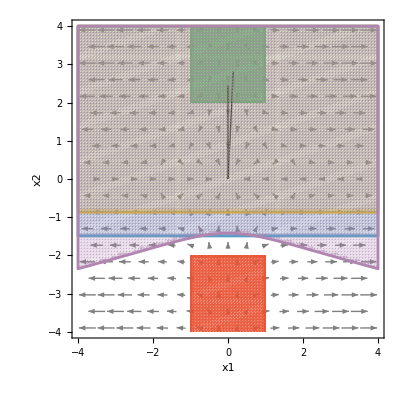

arch2-1

Variables: {x1,x2}

Flow: {-1.+x1^2+x2^2,-5.+5. x1 x2}

Initial: {-1.75-x1^2+4. x2-x2^2}

Unsafe: {-1.-x1,3.+x1,-2.-x2,3.+x2}

Using Bounded Case Characterization:

Verified at deg 3

-2.87732-1.04906 x1-0.21107 x1^2-0.23562 x1^3-0.0354 x2-0.05478 x1 x2-0.22575 x1^2 x2-0.0233 x2^2-0.35816 x1 x2^2-0.10354 x2^3

totalsdptime: 0.0183902

Using Sound Characterization: Verified, time used: 0.244462

Using Complete (polynomial) Characterization:

Verified at deg 3

-4.96704-2.08085 x1-0.66042 x1^2-0.45532 x1^3-0.01109 x2+0.06661 x1 x2-0.27629 x1^2 x2-0.0177 x2^2-0.5807 x1 x2^2-0.15415 x2^3

totalsdptime: 0.0240312

Using Complete (polynomial) Characterization: Verified, time used: 0.246176

Using Complete (semialgebraic) Characterization:

Verified at deg 3

-4.99161-0.95395 x1-2.98014 x1^2-0.87167 x1^3+1.06865 x2-0.57843 x1 x2+0.18096 x1^2 x2-0.15648 x2^2+0.34577 x1 x2^2-0.2912 x2^3-3.17646 √(1+x1^2+x2^2)-1.73545 x1 √(1+x1^2+x2^2)-1.18392 x1^2 √(1+x1^2+x2^2)-1.21472 x1^3 √(1+x1^2+x2^2)+0.7795 x2 √(1+x1^2+x2^2)+1.42516 x1 x2 √(1+x1^2+x2^2)-0.59492 x1^2 x2 √(1+x1^2+x2^2)+0.30888 x2^2 √(1+x1^2+x2^2)-0.9034 x1 x2^2 √(1+x1^2+x2^2)-0.11057 x2^3 √(1+x1^2+x2^2)

totalsdptime: 2.14965

Using Complete (semialgebraic) Characterization: Verified, time used: 7.39188

Plot2d...

-Graphics-

arch2-2

Variables: {x1,x2}

Flow: {-1+x1^2+x2^2,-5+5 x1 x2}

Initial: {-2+x1,-2-x2}

Unsafe: {-1-x1^2+x2,x2}

Using Bounded Case Characterization:

Verified at deg 3

0.47175-0.35804 x1+0.03715 x1^2-0.43538 x1^3+0.76826 x2-0.33546 x1 x2+0.09283 x1^2 x2+0.23706 x2^2-0.43035 x1 x2^2+0.18126 x2^3

totalsdptime: 0.0378901

Using Sound Characterization: Verified, time used: 0.238193

Using Complete (polynomial) Characterization:

Verified at deg 3

0.70474-1.37432 x1+0.05021 x1^2-0.91372 x1^3+1.53761 x2-0.49742 x1 x2+0.42761 x1^2 x2+0.37391 x2^2-0.71738 x1 x2^2+0.26556 x2^3

totalsdptime: 0.0227792

Using Complete (polynomial) Characterization: Verified, time used: 0.21102

Using Complete (semialgebraic) Characterization:

Verified at deg 3

-0.44559-1.21601 x1-0.55953 x1^2-1.22458 x1^3+3.03564 x2-0.72011 x1 x2+1.68672 x1^2 x2+0.39072 x2^2-1.18795 x1 x2^2+1.27804 x2^3+0.18702 √(1+x1^2+x2^2)-2.5135 x1 √(1+x1^2+x2^2)+0.17459 x1^2 √(1+x1^2+x2^2)-2.04508 x1^3 √(1+x1^2+x2^2)+1.75335 x2 √(1+x1^2+x2^2)-0.75966 x1 x2 √(1+x1^2+x2^2)+0.7515 x1^2 x2 √(1+x1^2+x2^2)+0.76017 x2^2 √(1+x1^2+x2^2)-2.0374 x1 x2^2 √(1+x1^2+x2^2)+0.55309 x2^3 √(1+x1^2+x2^2)

totalsdptime: 2.30151

Using Complete (semialgebraic) Characterization: Verified, time used: 7.53301

Plot2d...

-Graphics-

arch3-1

Variables: {x1,x2}

Flow: {x1-x1^3+x2-x1 x2^2,-x1+x2-x1^2 x2-x2^3}

Initial: {0.04-x1^2-x2^2}

Unsafe: {-12.25+5. x1-x1^2+5. x2-x2^2}

Using Bounded Case Characterization:

Verified at deg 2

-1.56667+0.16057 x1+0.43865 x1^2+0.17357 x2+0.06865 x1 x2+0.43026 x2^2

totalsdptime: 0.0126564

Using Sound Characterization: Verified, time used: 0.172557

Using Complete (polynomial) Characterization:

Verified at deg 2

-2.73238+0.35489 x1+0.78923 x1^2+0.38108 x2+0.14993 x1 x2+0.77639 x2^2

totalsdptime: 0.0143583

Using Complete (polynomial) Characterization: Verified, time used: 0.162984

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-6.50979+0.13336 x1-1.50017 x1^2+0.16059 x2+0.32875 x1 x2-1.51134 x2^2-3.23342 √(1+x1^2+x2^2)+0.41669 x1 √(1+x1^2+x2^2)+3.55693 x1^2 √(1+x1^2+x2^2)+0.44104 x2 √(1+x1^2+x2^2)+0.12369 x1 x2 √(1+x1^2+x2^2)+3.54843 x2^2 √(1+x1^2+x2^2)

totalsdptime: 1.99125

Using Complete (semialgebraic) Characterization: Verified, time used: 4.0065

Plot2d...

-Graphics-

arch3-2

Variables: {x1,x2}

Flow: {x1-x1^3+x2-x1 x2^2,-x1+x2-x1^2 x2-x2^3}

Initial: {-2+x1-x2^2,x2,x1}

Unsafe: {-2-x1^2-x2,-x2}

Using Bounded Case Characterization:

totalsdptime: 0.0651655

Using Sound Characterization: No valid soltion, time used: 1.04061

Using Complete (polynomial) Characterization:

totalsdptime: 0.231082

Using Complete (polynomial) Characterization: No valid soltion, time used: 1.32418

Using Complete (semialgebraic) Characterization:

Verified at deg 1

-0.00046-0.00005 x1-0.00025 x2

totalsdptime: 0.417221

Using Complete (semialgebraic) Characterization: Verified, time used: 0.422826

Plot2d...

-Graphics-

arch4-1

Variables: {x1,x2}

Flow: {-2. x1+x1^2+x2,x1-2. x2+x2^2}

Initial: {0.01-x1^2-x2^2}

Unsafe: {-1.0625+1.5 x1-x1^2+1.5 x2-x2^2}

Using Bounded Case Characterization:

totalsdptime: 0.0766398

Using Sound Characterization: No valid soltion, time used: 0.133719

Using Complete (polynomial) Characterization:

Verified at deg 5

-0.17689+0.38322 x1-16.4973 x1^2-11.2862 x1^3+2738.13 x1^4-1178.49 x1^5+0.38326 x2+32.1077 x1 x2+11.0933 x1^2 x2-4174.43 x1^3 x2+1159.64 x1^4 x2-16.4957 x2^2+11.0941 x1 x2^2+2873.85 x1^2 x2^2+18.6166 x1^3 x2^2-11.2882 x2^3-4174.31 x1 x2^3+18.428 x1^2 x2^3+2738.07 x2^4+1159.63 x1 x2^4-1178.44 x2^5

totalsdptime: 0.241469

Using Complete (polynomial) Characterization: Verified, time used: 0.955693

Using Complete (semialgebraic) Characterization:

Verified at deg 3

-15.4983-8.61919 x1-955.881 x1^2+505.52 x1^3-8.5701 x2+1879.02 x1 x2-515.543 x1^2 x2-955.854 x2^2-513.817 x1 x2^2+504.969 x2^3+15.2852 √(1+x1^2+x2^2)+9.21296 x1 √(1+x1^2+x2^2)+945.953 x1^2 √(1+x1^2+x2^2)-462.104 x1^3 √(1+x1^2+x2^2)+9.16444 x2 √(1+x1^2+x2^2)-1876.46 x1 x2 √(1+x1^2+x2^2)+462.473 x1^2 x2 √(1+x1^2+x2^2)+945.923 x2^2 √(1+x1^2+x2^2)+460.729 x1 x2^2 √(1+x1^2+x2^2)-461.52 x2^3 √(1+x1^2+x2^2)

totalsdptime: 2.96249

Using Complete (semialgebraic) Characterization: Verified, time used: 6.24044

Plot2d...

-Graphics-

arch4-2

Variables: {x1,x2}

Flow: {-2. x1+x1^2+x2,x1-2. x2+x2^2}

Initial: {0.5+x1-x1^2+x2-x2^2}

Unsafe: {-4.+x1 x2,-x1}

Using Bounded Case Characterization:

totalsdptime: 0.0458498

Using Sound Characterization: No valid soltion, time used: 1.16669

Using Complete (polynomial) Characterization:

Verified at deg 6

-3.63912-3.20403 x1-0.63097 x1^2-1.12308 x1^3+0.13987 x1^4-0.23287 x1^5-3.24372 x2-1.18781 x1 x2-1.55727 x1^2 x2-0.0133 x1^3 x2-0.19485 x1^4 x2-0.58353 x2^2-1.22873 x1 x2^2+0.53182 x1^2 x2^2-0.24274 x1^3 x2^2-0.80568 x2^3+0.12095 x1 x2^3-0.15668 x1^2 x2^3+0.00439 x2^4-0.00047 x1 x2^4-0.00001 x2^5

totalsdptime: 0.152611

Using Complete (polynomial) Characterization: Verified, time used: 1.35229

Using Complete (semialgebraic) Characterization:

totalsdptime: 4.24351

Plot2d...

-Graphics-

nagumo-1

Variables: {x1,x2}

Flow: {0.875+x1-0.333333 x1^3-x2,0.056+0.08 x1-0.064 x2}

Initial: {-2.0625-1.5 x1-x1^2+2.5 x2-x2^2}

Unsafe: {-8.0625-4.5 x1-x1^2-3.5 x2-x2^2}

Using Bounded Case Characterization:

Verified at deg 2

-1.31219-0.51094 x1+0.10891 x1^2-0.9441 x2+0.00081 x1 x2-0.24305 x2^2

totalsdptime: 0.0121923

Using Sound Characterization: Verified, time used: 0.130697

Using Complete (polynomial) Characterization:

Verified at deg 2

-2.78743-1.11423 x1+0.2312 x1^2-1.86668 x2+0.00048 x1 x2-0.46807 x2^2

totalsdptime: 0.0157925

Using Complete (polynomial) Characterization: Verified, time used: 0.141408

Using Complete (semialgebraic) Characterization:

Verified at deg 2

-4.53195-0.63812 x1-3.16623 x1^2-1.1438 x2+3.11897 x1 x2-2.34532 x2^2-4.05135 √(1+x1^2+x2^2)-2.32591 x1 √(1+x1^2+x2^2)+2.23514 x1^2 √(1+x1^2+x2^2)-3.75849 x2 √(1+x1^2+x2^2)+0.50693 x1 x2 √(1+x1^2+x2^2)-1.10516 x2^2 √(1+x1^2+x2^2)

totalsdptime: 2.04512

Using Complete (semialgebraic) Characterization: Verified, time used: 3.9339

Plot2d...

-Graphics-

nagumo-2

Variables: {x1,x2}

Flow: {0.875+x1-0.333333 x1^3-x2,0.056+0.08 x1-0.064 x2}

Initial: {-2.0625-1.5 x1-x1^2+2.5 x2-x2^2}

Unsafe: {-2.-x2}

Using Bounded Case Characterization:

totalsdptime: 0.246959

Using Sound Characterization: No valid soltion, time used: 1.46058

Using Complete (polynomial) Characterization:

Verified at deg 3

-0.00131-0.00041 x1+0.00011 x1^2-0.00188 x2+0.00007 x1 x2-0.00056 x2^2-0.00006 x2^3

totalsdptime: 0.0535949

Using Complete (polynomial) Characterization: Verified, time used: 0.16238

Using Complete (semialgebraic) Characterization:

totalsdptime: 13.8847

Plot2d...

-Graphics-

```mathematica
benchmarks={"vector-1","vector-2","barrier-1","barrier-2","lie-der-1","lie-der-2","arch1-1","arch1-2","arch2-1","arch2-2","arch3-1","arch3-2","arch4-1","arch4-2","nagumo-1","nagumo-2"};
For[i=1,i≤ 16,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
numTolerance = 0;
verifytime=600;
plot =1;
plotRange = {{-4,4},{-4,4}};
verifyResults[benchmarkname,1plot,plotRange,verifytime,numTolerance ];
]
```

```mathematica
benchmarks={"lorenz-1","lorenz-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
numTolerance = 0;
verifytime=600;
plot =1;
plotRange = {{-20,20},{-20,20},{-20,20}};
verifyResults[benchmarkname,plot,plotRange,verifytime,numTolerance];
]
```

lorenz-1

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-575.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-487.75-33. x1-x1^2-29. x2-x2^2+5. x3-x3^2}

Using Bounded Case Characterization:

Verify out of time at deg 6

-0.68869+0.00141 x1-0.1468 x1^2+0.65466 x1^3+0.07282 x1^4+0.00316 x1^5+0.00026 x1^6+0.00082 x2-0.13823 x1 x2+0.69036 x1^2 x2+0.0638 x1^3 x2+0.00184 x1^4 x2+0.02216 x2^2-0.08355 x1 x2^2-0.01386 x1^2 x2^2-0.00163 x1^3 x2^2+0.00003 x1^4 x2^2-0.16864 x2^3-0.03077 x1 x2^3-0.0008 x1^2 x2^3+0.00425 x2^4+0.00016 x1 x2^4-0.00002 x1^2 x2^4+0.00012 x2^5-0.00323 x3-0.01889 x1 x3-0.13785 x1^2 x3+0.01348 x1^3 x3-0.00233 x1^4 x3-0.00001 x1^5 x3-0.00545 x2 x3-0.0949 x1 x2 x3+0.01499 x1^2 x2 x3-0.00473 x1^3 x2 x3+0.02399 x2^2 x3-0.00459 x1 x2^2 x3+0.00155 x1^2 x2^2 x3+0.00001 x1^3 x2^2 x3-0.00508 x2^3 x3+0.00078 x1 x2^3 x3-0.00033 x2^4 x3+0.27432 x3^2+0.01481 x1 x3^2+0.00557 x1^2 x3^2-0.00194 x1^3 x3^2+0.00003 x1^4 x3^2+0.01312 x2 x3^2-0.02062 x1 x2 x3^2-0.00138 x1^2 x2 x3^2+0.01163 x2^2 x3^2+0.00051 x1 x2^2 x3^2-0.00004 x1^2 x2^2 x3^2+0.00033 x2^3 x3^2-0.00001 x1 x2^3 x3^2+0.00001 x2^4 x3^2-0.04307 x3^3-0.00751 x1 x3^3+0.00055 x1^2 x3^3+0.00001 x1^3 x3^3-0.00694 x2 x3^3+0.00094 x1 x2 x3^3-0.00062 x2^2 x3^3+0.00536 x3^4+0.0003 x1 x3^4-0.00002 x1^2 x3^4+0.00023 x2 x3^4-0.00001 x1 x2 x3^4+0.00001 x2^2 x3^4-0.00025 x3^5

totalsdptime: 0.122759

Using Sound Characterization: No valid soltion, time used: 699.296

Using Complete (polynomial) Characterization:

Verified at deg 4

-29.1343-0.07359 x1+0.1403 x1^2-0.00059 x1^3+0.00017 x1^4-0.03472 x2-0.03236 x1 x2-0.00025 x1^2 x2+0.09749 x2^2-0.0001 x1 x2^2-0.00004 x1^2 x2^2-0.0001 x2^3+0.00009 x2^4-6.8905 x3+0.01879 x1 x3-0.00203 x1^2 x3+0.00914 x2 x3+0.00003 x1 x2 x3-0.00899 x2^2 x3+0.34597 x3^2-0.00034 x1 x3^2-0.00004 x1^2 x3^2-0.00009 x2 x3^2+0.00017 x2^2 x3^2-0.00871 x3^3+0.00008 x3^4

totalsdptime: 0.314681

Using Complete (polynomial) Characterization: Verified, time used: 45.2209

Using Complete (semialgebraic) Characterization:

Verify out of time at deg 2

-10.7643-0.10858 x1+0.0459 x1^2+0.03499 x2-0.03235 x1 x2+0.02325 x2^2-1.00281 x3+0.01502 x1 x3-0.002 x2 x3+0.02991 x3^2+0.03942 √(1+x1^2+x2^2+x3^2)-0.00792 x1 √(1+x1^2+x2^2+x3^2)+0.00054 x1^2 √(1+x1^2+x2^2+x3^2)+0.00201 x2 √(1+x1^2+x2^2+x3^2)+0.00007 x1 x2 √(1+x1^2+x2^2+x3^2)-0.00011 x2^2 √(1+x1^2+x2^2+x3^2)-0.01154 x3 √(1+x1^2+x2^2+x3^2)-0.00008 x1 x3 √(1+x1^2+x2^2+x3^2)-0.00016 x3^2 √(1+x1^2+x2^2+x3^2)

totalsdptime: 0.585332

Using Complete (semialgebraic) Characterization: No valid soltion, time used: 627.337

Plot3d...

-Graphics3D-

lorenz-2

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-575.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-4.-0.01 x1^2-0.01 x2^2-x3,-x3}

Using Bounded Case Characterization:

ReplaceAll::reps: {Removed[$$Failure]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Verified at deg 5

-12.7974+0.02645 x1+0.04544 x1^2+0.00008 x1^3+0.00014 x1^4-0.02388 x2-0.01705 x1 x2+0.00021 x1^2 x2+0.072 x2^2+0.00004 x1 x2^2-0.00007 x1^2 x2^2-0.00015 x2^3+0.00009 x2^4-4.29786 x3-0.00209 x1 x3+0.00116 x1^2 x3+0.00735 x2 x3+0.00017 x1 x2 x3-0.00907 x2^2 x3+0.29954 x3^2-0.00008 x1^2 x3^2-0.00017 x2 x3^2-0.00001 x1 x2 x3^2+0.00018 x2^2 x3^2-0.00885 x3^3+0.00009 x3^4

totalsdptime: 0.0929478

Using Sound Characterization: Verified, time used: 196.556

Using Complete (polynomial) Characterization:

Verify out of time at deg 6

-10.7076+0.06357 x1-4.18809 x1^2+1.36767 x1^3+0.04813 x1^4+0.00385 x1^5+0.00031 x1^6+0.05777 x2-3.54513 x1 x2+1.5573 x1^2 x2-0.01035 x1^3 x2+0.00064 x1^4 x2+0.53264 x2^2-0.06166 x1 x2^2+0.05039 x1^2 x2^2-0.00097 x1^3 x2^2-0.00003 x1^4 x2^2-0.33012 x2^3-0.01424 x1 x2^3-0.00018 x1^2 x2^3+0.0008 x2^4-0.00002 x1 x2^4-0.00003 x1^2 x2^4+0.00002 x2^5+0.00002 x2^6-2.73743 x3+3.09583 x1 x3-1.82347 x1^2 x3-0.02987 x1^3 x3+0.00193 x1^4 x3+1.90219 x2 x3-1.39738 x1 x2 x3-0.0366 x1^2 x2 x3-0.00534 x1^3 x2 x3-0.30765 x2^2 x3+0.00995 x1 x2^2 x3+0.00178 x1^2 x2^2 x3+0.00596 x2^3 x3+0.00007 x1 x2^3 x3-0.00248 x2^4 x3+16.7943 x3^2-0.25162 x1 x3^2+0.11278 x1^2 x3^2-0.00033 x1^3 x3^2-0.00003 x1^4 x3^2-0.10169 x2 x3^2+0.01749 x1 x2 x3^2-0.00046 x1^2 x2 x3^2+0.11193 x2^2 x3^2+0.00006 x1 x2^2 x3^2-0.00005 x1^2 x2^2 x3^2+0.00019 x2^3 x3^2+0.00005 x2^4 x3^2-1.79762 x3^3+0.00621 x1 x3^3-0.00094 x1^2 x3^3-0.00402 x2 x3^3+0.00058 x1 x2 x3^3-0.00453 x2^2 x3^3+0.08523 x3^4-0.00002 x1^2 x3^4+0.0002 x2 x3^4+0.00005 x2^2 x3^4-0.00192 x3^5+0.00002 x3^6

totalsdptime: 1.00763

Using Complete (polynomial) Characterization: No valid soltion, time used: 717.918

Using Complete (semialgebraic) Characterization:

Verify out of time at deg 2

-1.31863-0.0007 x1+0.00355 x1^2-0.00017 x2-0.00864 x1 x2+0.00158 x2^2-0.18517 x3-0.00002 x1 x3+0.00011 x2 x3+0.01405 x3^2+0.04961 √(1+x1^2+x2^2+x3^2)+0.00016 x1 √(1+x1^2+x2^2+x3^2)+0.00013 x1^2 √(1+x1^2+x2^2+x3^2)+0.00001 x2 √(1+x1^2+x2^2+x3^2)+0.00002 x1 x2 √(1+x1^2+x2^2+x3^2)+0.00011 x2^2 √(1+x1^2+x2^2+x3^2)-0.01179 x3 √(1+x1^2+x2^2+x3^2)

totalsdptime: 0.635289

Using Complete (semialgebraic) Characterization: No valid soltion, time used: 603.462

Plot3d...

-Graphics3D-

```mathematica
benchmarks={"lotka-1","lotka-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
verifytime=600;
numTolerance = 0;
plot =1;
plotRange = {{-4,4},{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytime,numTolerance];
]
```

lotka-1

Variables: {x1,x2,x3}

Flow: {x1-x1 x3,x2-2. x2 x3,-x3+x1 x3+x2 x3}

Initial: {-4.16+2. x1-x1^2+2. x2-x2^2+3. x3-x3^2}

Unsafe: {-4.16-2. x1-x1^2-2. x2-x2^2-3. x3-x3^2}

Using Bounded Case Characterization:

totalsdptime: 0.127272

Using Sound Characterization: No valid soltion, time used: 99.6069

Using Complete (polynomial) Characterization:

totalsdptime: 0.704444

Using Complete (polynomial) Characterization: No valid soltion, time used: 38.8923

Using Complete (semialgebraic) Characterization:

Verify out of time at deg 3

-0.61097+0.09561 x1-0.0687 x1^2+0.00806 x1^3-0.04855 x2-0.02775 x1 x2+0.00513 x1^2 x2-0.04147 x2^2+0.00723 x1 x2^2+0.0039 x2^3-0.56467 x3-0.02727 x1 x3+0.00162 x1^2 x3-0.03763 x2 x3+0.00202 x1 x2 x3+0.0049 x2^2 x3+0.0069 x3^2+0.00445 x1 x3^2+0.00262 x2 x3^2-0.00662 x3^3+0.03443 √(1+x1^2+x2^2+x3^2)-0.08892 x1 √(1+x1^2+x2^2+x3^2)+0.00265 x1^2 √(1+x1^2+x2^2+x3^2)-0.00016 x1^3 √(1+x1^2+x2^2+x3^2)-0.03686 x2 √(1+x1^2+x2^2+x3^2)+0.00128 x1 x2 √(1+x1^2+x2^2+x3^2)-0.00013 x1^2 x2 √(1+x1^2+x2^2+x3^2)+0.0018 x2^2 √(1+x1^2+x2^2+x3^2)-0.00013 x1 x2^2 √(1+x1^2+x2^2+x3^2)-0.00005 x2^3 √(1+x1^2+x2^2+x3^2)+0.05543 x3 √(1+x1^2+x2^2+x3^2)+0.00268 x1 x3 √(1+x1^2+x2^2+x3^2)-0.00003 x1^2 x3 √(1+x1^2+x2^2+x3^2)+0.00318 x2 x3 √(1+x1^2+x2^2+x3^2)-0.00021 x1 x2 x3 √(1+x1^2+x2^2+x3^2)+0.00001 x2^2 x3 √(1+x1^2+x2^2+x3^2)+0.00048 x3^2 √(1+x1^2+x2^2+x3^2)-0.00022 x1 x3^2 √(1+x1^2+x2^2+x3^2)-0.00006 x2 x3^2 √(1+x1^2+x2^2+x3^2)+0.00017 x3^3 √(1+x1^2+x2^2+x3^2)

totalsdptime: 7.13836

Using Complete (semialgebraic) Characterization: No valid soltion, time used: 662.078

Plot3d...

-Graphics3D-

lotka-2

Variables: {x1,x2,x3}

Flow: {x1-x1 x3,x2-2. x2 x3,-x3+x1 x3+x2 x3}

Initial: {-2.91+2. x1-x1^2+2. x2-x2^2-2. x3-x3^2}

Unsafe: {-x1^2-x2^2+x3}

Using Bounded Case Characterization:

totalsdptime: 0.189836

Using Sound Characterization: No valid soltion, time used: 0.19934

Using Complete (polynomial) Characterization:

totalsdptime: 0.890453

Using Complete (polynomial) Characterization: No valid soltion, time used: 451.583

Using Complete (semialgebraic) Characterization:

Verify out of time at deg 3

-0.00024-0.01149 x1+0.00975 x1^2-0.00388 x1^3+0.00119 x2-0.00013 x1 x2+0.00071 x1^2 x2-0.00004 x2^2-0.00224 x1 x2^2+0.00235 x2^3+0.00419 x3-0.01085 x1 x3+0.01428 x1^2 x3-0.0037 x2 x3+0.00732 x1 x2 x3-0.00136 x2^2 x3-0.0046 x3^2-0.01569 x1 x3^2-0.00112 x2 x3^2-0.00074 x3^3+0.00074 √(1+x1^2+x2^2+x3^2)+0.01126 x1 √(1+x1^2+x2^2+x3^2)-0.01393 x1^2 √(1+x1^2+x2^2+x3^2)+0.00103 x1^3 √(1+x1^2+x2^2+x3^2)-0.00136 x2 √(1+x1^2+x2^2+x3^2)-0.00006 x1 x2 √(1+x1^2+x2^2+x3^2)+0.00103 x1^2 x2 √(1+x1^2+x2^2+x3^2)-0.00308 x2^2 √(1+x1^2+x2^2+x3^2)+0.00009 x1 x2^2 √(1+x1^2+x2^2+x3^2)+0.00017 x2^3 √(1+x1^2+x2^2+x3^2)-0.00113 x3 √(1+x1^2+x2^2+x3^2)+0.00754 x1 x3 √(1+x1^2+x2^2+x3^2)+0.00091 x1^2 x3 √(1+x1^2+x2^2+x3^2)+0.00107 x2 x3 √(1+x1^2+x2^2+x3^2)-0.00392 x1 x2 x3 √(1+x1^2+x2^2+x3^2)+0.0033 x2^2 x3 √(1+x1^2+x2^2+x3^2)+0.00552 x3^2 √(1+x1^2+x2^2+x3^2)-0.00021 x1 x3^2 √(1+x1^2+x2^2+x3^2)-0.00005 x2 x3^2 √(1+x1^2+x2^2+x3^2)+0.00001 x3^3 √(1+x1^2+x2^2+x3^2)

totalsdptime: 10.5524

Using Complete (semialgebraic) Characterization: No valid soltion, time used: 615.539

Plot3d...

-Graphics3D-

```mathematica
benchmarks={"lyapunov-1","lyapunov-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
numTolerance = 0;
verifytime=600;
plot =1;
plotRange = {{-4,4},{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytime,numTolerance ];
]
```

lyapunov-1

Variables: {x1,x2,x3}

Flow: {-x2,-x3,-x1+x1^3-2. x2-x3}

Initial: {0.0625+0.5 x1-x1^2+0.5 x2-x2^2+0.5 x3-x3^2}

Unsafe: {-6.5+3. x1-x1^2-3. x2-x2^2-3. x3-x3^2}

Using Bounded Case Characterization:

Verify out of time at deg 5

-1.47914-0.05061 x1-0.95921 x1^2-0.05532 x1^3+0.89006 x1^4+0.11092 x1^5-0.211 x2-1.28674 x1 x2-0.22624 x1^2 x2+1.07371 x1^3 x2-0.1037 x1^4 x2-0.44701 x2^2+0.33868 x1 x2^2+1.01272 x1^2 x2^2+0.02736 x1^3 x2^2-0.148 x2^3+0.82941 x1 x2^3-0.00105 x1^2 x2^3+0.13541 x2^4-0.00053 x1 x2^4-0.00002 x2^5-0.17555 x3-0.45344 x1 x3-0.26069 x1^2 x3-1.2831 x1^3 x3-0.00001 x1^4 x3+1.25934 x2 x3+0.35433 x1 x2 x3-0.23921 x1^2 x2 x3-0.14637 x2^2 x3-0.56768 x1 x2^2 x3+0.00002 x1^2 x2^2 x3+0.06514 x2^3 x3-0.00001 x2^4 x3+0.12251 x3^2+0.05937 x1 x3^2+0.73377 x1^2 x3^2-0.01054 x2 x3^2+0.25329 x1 x2 x3^2-0.00001 x1^2 x2 x3^2-0.0525 x2^2 x3^2-0.00487 x3^3-0.28695 x1 x3^3+0.04597 x2 x3^3+0.01079 x3^4

totalsdptime: 0.107815

Using Sound Characterization: No valid soltion, time used: 880.172

Using Complete (polynomial) Characterization:

Verify out of time at deg 5

-4.52933-0.17827 x1-2.7448 x1^2+0.25921 x1^3+2.66074 x1^4+0.08589 x1^5-0.65554 x2-2.89962 x1 x2-0.47598 x1^2 x2+3.07849 x1^3 x2-0.13416 x1^4 x2-1.4895 x2^2+0.53361 x1 x2^2+2.704 x1^2 x2^2+0.04796 x1^3 x2^2-0.40422 x2^3+2.26221 x1 x2^3-0.00096 x1^2 x2^3+0.47177 x2^4-0.00013 x1 x2^4-0.00002 x2^5-0.42456 x3-1.46506 x1 x3-0.67288 x1^2 x3-3.10853 x1^3 x3+4.43643 x2 x3+0.39618 x1 x2 x3-1.65671 x1^2 x2 x3-0.32551 x2^2 x3-1.4135 x1 x2^2 x3+0.03541 x2^3 x3+0.75394 x3^2+0.14695 x1 x3^2+1.36094 x1^2 x3^2+0.08162 x2 x3^2+0.67508 x1 x2 x3^2-0.0434 x2^2 x3^2-0.01033 x3^3-0.37619 x1 x3^3+0.03682 x2 x3^3+0.00433 x3^4

totalsdptime: 0.611837

Using Complete (polynomial) Characterization: No valid soltion, time used: 799.277

Using Complete (semialgebraic) Characterization:

Verify out of time at deg 2

-5.7422+0.0014 x1-0.63256 x1^2-0.73559 x2-2.15055 x1 x2+0.66824 x2^2-0.88881 x3-0.00566 x1 x3+5.71021 x2 x3+0.59282 x3^2-3.18368 √(1+x1^2+x2^2+x3^2)+0.87421 x1 √(1+x1^2+x2^2+x3^2)+2.66382 x1^2 √(1+x1^2+x2^2+x3^2)-0.92029 x2 √(1+x1^2+x2^2+x3^2)+3.16929 x1 x2 √(1+x1^2+x2^2+x3^2)+0.1198 x2^2 √(1+x1^2+x2^2+x3^2)-0.02079 x3 √(1+x1^2+x2^2+x3^2)-3.57377 x1 x3 √(1+x1^2+x2^2+x3^2)+0.31556 x2 x3 √(1+x1^2+x2^2+x3^2)+0.11191 x3^2 √(1+x1^2+x2^2+x3^2)

totalsdptime: 5.86048

Using Complete (semialgebraic) Characterization: No valid soltion, time used: 632.028

Plot3d...

-Graphics3D-

lyapunov-2

Variables: {x1,x2,x3}

Flow: {-x2,-x3,-x1+x1^3-2. x2-x3}

Initial: {0.0625+0.5 x1-x1^2+0.5 x2-x2^2+0.5 x3-x3^2}

Unsafe: {-2.+x1,-2.-x2,-2.-x3}

Using Bounded Case Characterization:

Verify out of time at deg 6

-1.46651-0.10414 x1-0.99858 x1^2+0.05262 x1^3-0.94336 x1^4-0.01434 x1^5+1.21276 x1^6-0.21369 x2-0.28734 x1 x2+0.06099 x1^2 x2-0.41661 x1^3 x2-0.30637 x1^4 x2+0.49253 x1^5 x2-0.56912 x2^2-0.0103 x1 x2^2-0.35335 x1^2 x2^2+0.09392 x1^3 x2^2+1.57946 x1^4 x2^2-0.2099 x2^3-0.21445 x1 x2^3-0.29665 x1^2 x2^3+1.32011 x1^3 x2^3+0.08792 x2^4-0.02301 x1 x2^4+0.78816 x1^2 x2^4-0.068 x2^5+0.19104 x1 x2^5+0.02401 x2^6-0.11946 x3-0.05796 x1 x3+0.06769 x1^2 x3-1.06381 x1^3 x3-0.0968 x1^4 x3-0.74284 x1^5 x3+0.57937 x2 x3+0.02888 x1 x2 x3+2.55984 x1^2 x2 x3+0.1896 x1^3 x2 x3-0.36816 x1^4 x2 x3-0.1183 x2^2 x3-1.28697 x1 x2^2 x3-0.15928 x1^2 x2^2 x3-0.44232 x1^3 x2^2 x3+1.27195 x2^3 x3+0.06272 x1 x2^3 x3-0.08793 x1^2 x2^3 x3-0.03697 x2^4 x3-0.03606 x1 x2^4 x3+0.00013 x2^5 x3+0.03638 x3^2-0.0343 x1 x3^2+0.29227 x1^2 x3^2+0.16329 x1^3 x3^2+0.44341 x1^4 x3^2+0.08833 x2 x3^2+0.00489 x1 x2 x3^2-0.08273 x1^2 x2 x3^2+0.09291 x1^3 x2 x3^2-0.36331 x2^2 x3^2+0.05108 x1 x2^2 x3^2+0.10068 x1^2 x2^2 x3^2-0.00119 x2^3 x3^2-0.00364 x1 x2^3 x3^2+0.00016 x2^4 x3^2-0.02121 x3^3-0.24029 x1 x3^3-0.07833 x1^2 x3^3-0.13507 x1^3 x3^3+0.53508 x2 x3^3+0.01649 x1 x2 x3^3-0.00499 x1^2 x2 x3^3-0.00185 x2^2 x3^3-0.01044 x1 x2^2 x3^3+0.00004 x2^3 x3^3-0.04721 x3^4+0.0113 x1 x3^4+0.02031 x1^2 x3^4-0.00098 x2 x3^4-0.0003 x1 x2 x3^4+0.00032 x2^2 x3^4-0.00047 x3^5-0.00148 x1 x3^5+0.00002 x2 x3^5+0.00004 x3^6

totalsdptime: 0.19914

Using Sound Characterization: No valid soltion, time used: 219.796

Using Complete (polynomial) Characterization:

Verify out of time at deg 6

-3.58346-0.2958 x1-4.11368 x1^2-0.0763 x1^3+0.14228 x1^4-0.04309 x1^5+2.11589 x1^6-0.51446 x2-1.02957 x1 x2-0.27757 x1^2 x2+0.3528 x1^3 x2-0.1774 x1^4 x2+1.94978 x1^5 x2-4.00141 x2^2-0.13146 x1 x2^2-1.27829 x1^2 x2^2-0.0678 x1^3 x2^2+4.52747 x1^4 x2^2-0.38873 x2^3+0.07557 x1 x2^3-0.38141 x1^2 x2^3+3.4471 x1^3 x2^3-1.3701 x2^4-0.07482 x1 x2^4+3.45396 x1^2 x2^4-0.23694 x2^5+1.39785 x1 x2^5+0.45744 x2^6-0.29481 x3+0.79358 x1 x3-0.14583 x1^2 x3-2.48933 x1^3 x3-0.06023 x1^4 x3-3.6178 x1^5 x3+3.59871 x2 x3+0.16305 x1 x2 x3+3.32842 x1^2 x2 x3+0.20893 x1^3 x2 x3-2.31801 x1^4 x2 x3-0.14412 x2^2 x3-0.48198 x1 x2^2 x3-0.05336 x1^2 x2^2 x3-5.84219 x1^3 x2^2 x3+3.32823 x2^3 x3+0.2053 x1 x2^3 x3-1.93831 x1^2 x2^3 x3-0.07322 x2^4 x3-1.47155 x1 x2^4 x3+0.00731 x2^5 x3-0.21118 x3^2+0.13257 x1 x3^2+2.09491 x1^2 x3^2+0.28241 x1^3 x3^2+3.49636 x1^4 x3^2-0.02667 x2 x3^2-0.51649 x1 x2 x3^2+0.07113 x1^2 x2 x3^2+2.80978 x1^3 x2 x3^2-0.95615 x2^2 x3^2+0.09539 x1 x2^2 x3^2+3.55728 x1^2 x2^2 x3^2+0.04887 x2^3 x3^2+0.51951 x1 x2^3 x3^2-0.00488 x2^4 x3^2-0.10647 x3^3-1.0728 x1 x3^3-0.1963 x1^2 x3^3-2.74265 x1^3 x3^3+1.79151 x2 x3^3-0.20203 x1 x2 x3^3-0.72853 x1^2 x2 x3^3-0.07039 x2^2 x3^3-0.7069 x1 x2^2 x3^3+0.00835 x2^3 x3^3+0.64722 x3^4+0.10773 x1 x3^4+0.4191 x1^2 x3^4+0.04471 x2 x3^4+0.27189 x1 x2 x3^4-0.00467 x2^2 x3^4-0.01217 x3^5-0.06319 x1 x3^5+0.00205 x2 x3^5+0.00042 x3^6

totalsdptime: 1.31514

Using Complete (polynomial) Characterization: No valid soltion, time used: 178.998

Using Complete (semialgebraic) Characterization:

```mathematica
benchmarks={"lorenz-1","lorenz-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
numTolerance = 1;
verifytime=600;
plot =1;
plotRange = {{-20,20},{-20,20},{-20,20}};
verifyResults[benchmarkname,plot,plotRange,verifytime,numTolerance];
]
```

lorenz-1

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-575.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-487.75-33. x1-x1^2-29. x2-x2^2+5. x3-x3^2}

Using Bounded Case Characterization:

$Aborted